1266

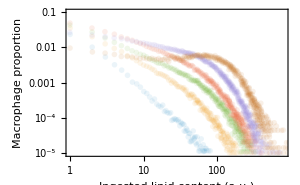

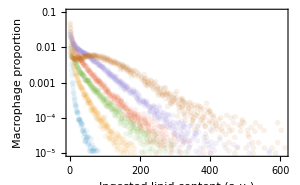

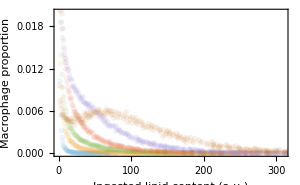

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.1;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,410},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[loglikelihood];

loglikelihood[{e_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,loglikelihoodL,outcome,λ,Loutput},


rhsVecfunction[v_?VectorQ,βvec_?VectorQ,n_?IntegerQ]:=Module[{x,h}, (* Here v = (m[0], m[1], ..., m[imax] *)
x=βvec*v;
h=ListConvolve[fvec,ListConvolve[x,v,{1,-1},0],{1,-1},0];
Take[h,n]-x
];

pmf[i_?NumericQ,μ_?NumericQ,sig_?NumericQ]:=Module[{σ2,μLog,σLog,dist},σ2=Log[1+(sig^2/μ^2)];
μLog=Log[μ]-σ2/2;
σLog=Sqrt[σ2];
dist=LogNormalDistribution[μLog,σLog];
CDF[dist,i+1]-CDF[dist,i]];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));


(*ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(pmf[#,e,cv*e]&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]+Last[βvec]*(1-Total[u[t]])),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,5}];

loglikelihoodm=Sum[1/Length[resamples[[j]]]*Sum[-Log[resamples[[j]][[i]][[2]]*(1-resamples[[j]][[i]][[2]])*(σm*Sqrt[12*(j-1)])*Sqrt[2 Pi]]-1/(2*(σm*Sqrt[12*(j-1)])^2)*(Log[resamples[[j]][[i]][[2]]/(1-resamples[[j]][[i]][[2]])]-Log[moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]]/(1-moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]])])^2,{i,1,Length[resamples[[j]]]}],{j,2,5}];

If[outcome==0&&Element[loglikelihoodM+loglikelihoodm,Reals],loglikelihoodM+loglikelihoodm,-10^(6)]
]

(* Plot function *)

plots[{e_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,modeldistributionplotloglinear,modeldistributionplotloglog},



rhsVecfunction[v_?VectorQ,βvec_?VectorQ,n_?IntegerQ]:=Module[{x,h}, (* Here v = (m[0], m[1], ..., m[imax] *)
x=βvec*v;
h=ListConvolve[fvec,ListConvolve[x,v,{1,-1},0],{1,-1},0];
Take[h,n]-x
];

pmf[i_?NumericQ,μ_?NumericQ,sig_?NumericQ]:=Module[{σ2,μLog,σLog,dist},σ2=Log[1+(sig^2/μ^2)];
μLog=Log[μ]-σ2/2;
σLog=Sqrt[σ2];
dist=LogNormalDistribution[μLog,σLog];
CDF[dist,i+1]-CDF[dist,i]];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)

(*ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(pmf[#,e,cv*e]&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]+Last[βvec]*(1-Total[u[t]])),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),0.1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];

modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,50},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,50},PlotRange->{{-0.5,50},{-0.05,50}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean lipid content (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];

Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot]},{Show[distributionlinearplot48,modeldistributionplot],Show[distributionloglinearplot48,modeldistributionplotloglinear],Show[distributionloglogplot48,modeldistributionplotloglog]}}]
]
```

```mathematica
(* MLE: βvec = β0 *)
nstep=1;
{eval,cvval,β0val,σMval,σmval}={0.391055971021132,0.9985182335437923,0.6669361808344381,0.8177854153254487,0.14661385533963045};
NMaximize[{loglikelihood[{100*e,cv,β0/100,0,1,σM,σm}],0.01<e<1,0.01<cv<10,0.1<β0<10,0.01<σM<3,0.01<σm<1},{e,cv,β0,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,σM,σm},loglikelihood[{100*e,cv,β0/100,0,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.333041,1.42145,0.753503,0.936916,0.134609},33.0482}

{33.2053,{e→0.331246,cv→1.72557,β0→0.72874,σM→0.812536,σm→0.127259}}

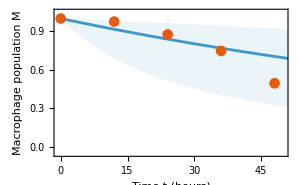
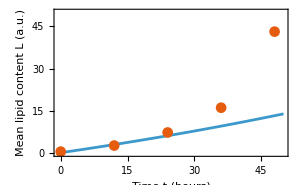
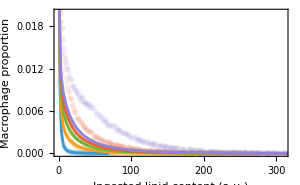
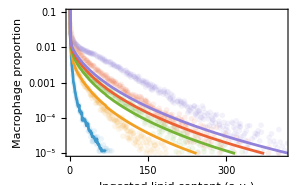
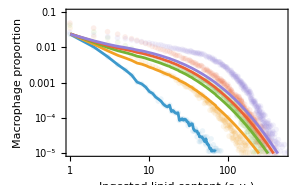
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0/100,0,1,σM,σm}/.{e->0.3312463068406558,cv->1.7255721876071861,β0->0.728740045994776,σM->0.8125359972505257,σm->0.12725852695621526}]
```

```mathematica
(* MLE: βvec = β0*Exp[β1*t] *)
nstep=1;
{eval,cvval,β0val,β1val,σMval,σmval}={0.5669519733495484,0.1,0.25123618837707296,0.0530161581687254,0.3299776196511747,0.05377237633255394};
NMaximize[{loglikelihood[{100*e,cv,β0/100,β1,1,σM,σm}],0.01<e<1,0.01<cv<2,0.01<β0<1,0.01<β1<1,0.01<σM<3,0.01<σm<1},{e,cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,β1,σM,σm},loglikelihood[{100*e,cv,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.483387,0.569452,0.339647,0.0451991,0.720903,0.187781},33.9847}

Current x: {{0.330554,1.05458,0.420461,0.0431492,1.38717,0.0877774},34.3968}

{39.924,{e→0.423536,cv→1.07155,β0→0.161817,β1→0.0730396,σM→0.178172,σm→0.108198}}

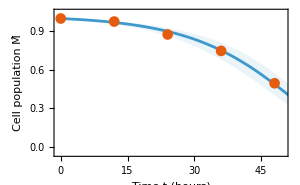
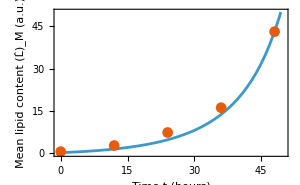
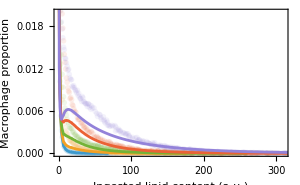
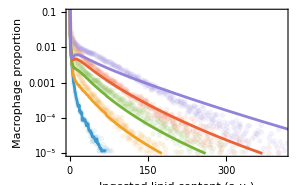
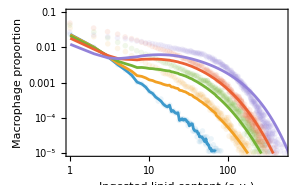
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0/100,β1,1,σM,σm}/.{e->0.4235357604353603,cv->1.0715501553629032,β0->0.16181715079582648,β1->0.07303959804015718,σM->0.17817214782777524,σm->0.10819795144125341}]
```

```mathematica
(* MLE: βvec = β0+β1*idx *)
nstep=1;
{eval,cvval,β0val,β1val,σMval,σmval}={0.12177390388387464,0.8,1.5592251365614875,0.16509286494405248,1.3337895859782167,0.08935303066888678};
NMaximize[{loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σm}],0.01<e<1,0.01<cv<2,0.1<β0<10,0.01<β1<1,0.01<σM<3,0.01<σm<1},{e,cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,β1,σM,σm},loglikelihood[{100*e,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.262031,0.666851,0.610113,0.0829098,1.318,0.129665},33.0731}

Current x: {{0.28239,0.670294,0.620899,0.0713485,1.28732,0.109871},33.2493}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

{34.5921,{e→0.292099,cv→1.20718,β0→0.318377,β1→0.139508,σM→0.438407,σm→0.17233}}

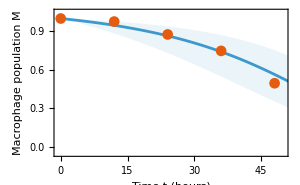
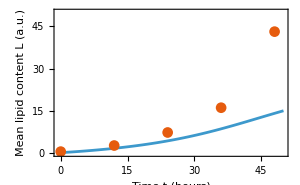
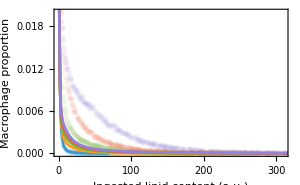
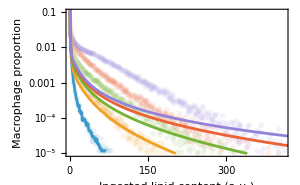
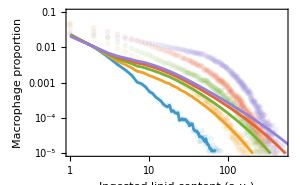
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0/100,β1/100,1,σM,σm}/.{e->0.2920987303977517,cv->1.2071777574060776,β0->0.318377499738081,β1->0.13950806683346417,σM->0.4384070383153057,σm->0.1723303384355372}]
```

```mathematica
(* MLE: βvec = β1/(1+(β1-β0)/β0*Exp[-t/q] - independent of cv! tends to β1->infinity case *)
nstep=1;
{eval,cvval,β0val,β1val,qval,σMval,σmval}={0.74270049747501,0.1,0.09155846845171661,0.9964731101780913,5.334136205905133,0.4778165611630636,0.22784210170928543};
NMaximize[{loglikelihood[{100*e,cv,β0/100,β1/100,q,σM,σm}],0.01<e<1,0.01<cv<2,0.01<β0<1,0.1<β1<100,0.01<q<100,0.01<σM<3,0.01<σm<1},{e,cv,β0,β1,q,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,β1,q,σM,σm},loglikelihood[{100*e,cv,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.454042,1.3172,0.156352,70.8673,13.3083,0.172673,0.128131},39.7184}

{39.7185,{e→0.453664,cv→1.32276,β0→0.156501,β1→70.6596,q→13.3101,σM→0.17313,σm→0.127658}}

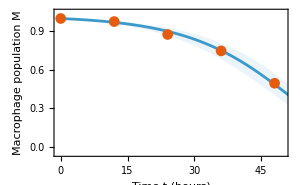
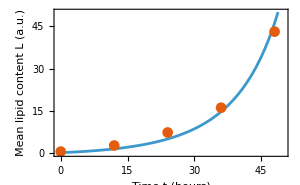
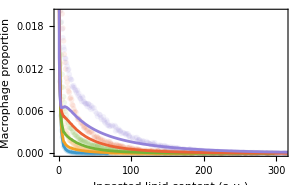
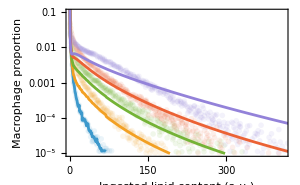
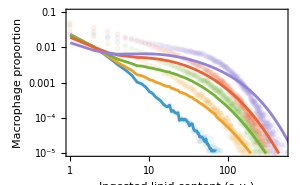
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0/100,β1/100,q,σM,σm}/.{e->0.45366350127741173,cv->1.3227627786035243,β0->0.15650136305887635,β1->70.65957760634981,q->13.310116516552911,σM->0.17312953179580065,σm->0.12765758643407843}]
```

```mathematica
(* MLE: βvec = β0+(β1-β0)*(1-Exp[-idx/q] *)
nstep=1;
{eval,cvval,β0val,β1val,qval,σMval,σLval}={0.14790624221009246,0.14249866574071965,1.1513887463275798,0.6732543174865205,3.283709978027588,1.4806159488920347,0.024993724556705354};
NMaximize[{loglikelihood[{100*e,cv,β0/100,β1,100*q,σM,σL}],0.01<e<1,0.01<cv<1,0.01<β0<10,0.01<β1<10,0.01<q<10,0.01<σM<3,0.01<σL<1},{e,cv,β0,β1,q,σM,σL},Method->{Automatic,"InitialPoints"->{{eval,cvval,β0val,β1val,qval,σMval,σLval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,cv,β0,β1,q,σM,σL},loglikelihood[{100*e,cv,β0/100,β1,100*q,σM,σL}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.167898,0.223932,1.89167,0.324496,3.20433,1.65772,0.170706},25.9082}

Current x: {{0.230237,0.146367,1.08432,0.289827,2.60622,1.6702,0.164338},28.6057}

Current x: {{0.259158,0.126374,0.5275,0.36111,2.06054,1.60954,0.230561},29.8296}

Current x: {{0.335129,0.351547,0.292608,0.373344,2.726,0.481627,0.166362},34.2134}

Current x: {{0.29648,0.352113,0.315857,0.445908,2.86901,0.454852,0.155498},34.4309}

Current x: {{0.305038,0.404865,0.160497,0.790045,3.01985,0.28049,0.217295},35.1942}

Current x: {{0.277476,0.444465,0.0613973,1.29605,3.29717,0.2,0.290302},35.6333}

Current x: {{0.261543,0.441507,0.0667722,1.34933,3.39899,0.1984,0.27703},35.6814}

Current x: {{0.242346,0.446931,0.0563294,1.55611,3.62472,0.186638,0.272973},35.7113}

{35.7899,{e→0.266609,cv→0.413903,β0→0.0450142,β1→1.54313,q→3.64413,σM→0.167823,σL→0.317911}}

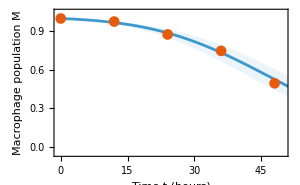
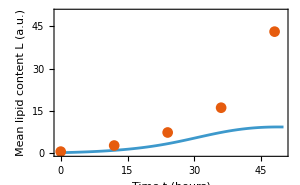
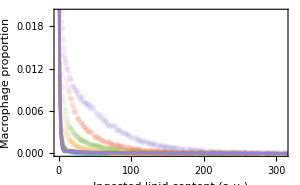
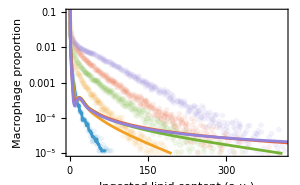
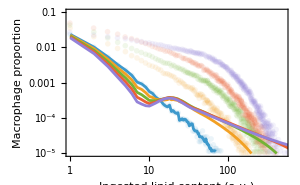
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{100*e,cv,β0/100,β1,100*q,σM,σL}/.{e->0.26660878394560306,cv->0.4139027199433241,β0->0.04501415430341984,β1->1.5431275524328947,q->3.6441316989274335,σM->0.16782306644744013,σL->0.3179110225867979}]
```